# Auxiliary Functions

```mathematica
Quiet@Remove["Global`*"]
FormattingStrings[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"phiNF"->"{phiNF}"];
auxiliarystring=StringReplace[auxiliarystring,"psiNF"->"{psiNF}"];
auxiliarystring=ToExpression[auxiliarystring,TeXForm];
Return[auxiliarystring]
]
FormattingStringsCommaSplit[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"phiNF"->"{phiNF}"];
auxiliarystring=StringReplace[auxiliarystring,"psiNF"->"{psiNF}"];
auxiliarystring=StringSplit[auxiliarystring,","];
Return[auxiliarystring]
]
```

## Vector field and equilibrium point

```mathematica
SetDirectory[NotebookDirectory[]];
null[_String]:=Null;
eqbool=1;
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
Print["The file 'Fixed parameter values.txt' could not be found. Run the Python script first."];
Quit[];
]
fixedpar={};
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=ReadLine["Fixed parameter values.txt"];
aux=FormattingStringsCommaSplit[aux];
parname=ToExpression[aux[[1]],TeXForm];
parval=ToExpression[aux[[2]],TeXForm];
AppendTo[fixedpar,parname->parval];
];
Close["Fixed parameter values.txt"];
]
ii[n_,x_]=√(π/(2x))*BesselI[n+1/2,x];
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
Print["The file 'Kinetics.txt' could not found. Run the Python script first."];
Quit[];
]
nvar=nvar/2;
kinetics=Range[2*nvar];
var=Range[2*nvar];
For[varnum=1,varnum<=2*nvar,varnum++,
kinetics[[varnum]]=ReadLine["Kinetics.txt"];
kinetics[[varnum]]=FormattingStrings[kinetics[[varnum]]];
If[FileExistsQ["List of variables.txt"],
var[[varnum]]=ReadLine["List of variables.txt"];
,
Print["The file 'List of variables.txt' could not be found. Run the Python script first."];
Quit[]
];
var[[varnum]]=ToExpression[var[[varnum]],TeXForm];
];
Close["Kinetics.txt"];
Close["List of variables.txt"];
Bmatrix=-D[kinetics[[1;;nvar]],{var[[1;;nvar]]}];
Kmatrix=D[kinetics[[nvar+1;;2*nvar]],{var[[1;;nvar]]}];
If[FileExistsQ["Diffusion matrix for Mathematica.json"],
Diffusionmatrix=Import["Diffusion matrix for Mathematica.json"];
Diffusionmatrix=ToExpression[Diffusionmatrix,TeXForm];
,
Print["The file 'Diffusion matrix for Mathematica.json' could not found. Run the Python script first."];
Quit[];
]
Diffbulk=Diffusionmatrix[[1;;nvar,1;;nvar]];
omega=DiagonalMatrix[Table[√((Bmatrix[[varnum]][[varnum]])/Diffbulk[[varnum,varnum]]),{varnum,nvar}]];
i0omegaR=DiagonalMatrix[Table[ii[0,omega[[varnum,varnum]]*R],{varnum,nvar}]];
i0primeomegaR=DiagonalMatrix[Table[D[ii[0,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
ilomegaR=DiagonalMatrix[Table[ii[l,omega[[varnum,varnum]]*R],{varnum,nvar}]];
ilprimeomegaR=DiagonalMatrix[Table[D[ii[l,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
S0=Dot[Inverse[Dot[Diffbulk,i0primeomegaR,omega]+Dot[Kmatrix,i0omegaR]],Kmatrix];
Sl=Dot[Inverse[Dot[Diffbulk,ilprimeomegaR,omega]+Dot[Kmatrix,ilomegaR]],Kmatrix];
If[eqbool==1,
eqs=Solve[kinetics[[nvar+1;;2*nvar]]==0/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]/.fixedpar,var[[nvar+1;;2*nvar]]];
Print[eqs];
If[Length[eqs]>1,
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
eqnumber=1];
eq=eqs[[eqnumber]];
,
eq={0};
]
(*Third equilibrium*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u→0.331701/δ+((1.62382×10^-19-2.81254×10^-19 ⅈ) (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2))/(δ (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))-1/δ(1.02294×10^-19+1.77179×10^-19 ⅈ) (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3),v→1/δ 2.42451×10^-17 (8.57889×10^17+(3.47726×10^35-6.02279×10^35 ⅈ)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)-((1.6536×10^32-2.86413×10^32 ⅈ) δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)-((3.36003×10^34-5.81975×10^34 ⅈ) c δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)+(0.132283+0.229122 ⅈ) (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))},{u→0.331701/δ+((1.62382×10^-19+2.81254×10^-19 ⅈ) (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2))/(δ (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))-1/δ(1.02294×10^-19-1.77179×10^-19 ⅈ) (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3),v→1/δ 2.42451×10^-17 (8.57889×10^17+(3.47726×10^35+6.02279×10^35 ⅈ)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)-((1.6536×10^32+2.86413×10^32 ⅈ) δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)-((3.36003×10^34+5.81975×10^34 ⅈ) c δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)+(0.132283-0.229122 ⅈ) (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))},{u→0.331701/δ-(3.24764×10^-19 (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2))/(δ (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))+1/δ 2.04588×10^-19 (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3),v→1/δ 2.42451×10^-17 (8.57889×10^17-6.95452×10^35/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)+(3.30721×10^32 δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)+(6.72007×10^34 c δ^2)/(4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3)-0.264567 (4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2+√((4.26184×10^54+1.85926×10^54 δ^2-6.17725×10^53 c δ^2)^2+4. (-1.65594×10^36+7.8748×10^32 δ^2+1.60012×10^35 c δ^2)^3))^(1/3))}}

# Fixed parameters and Turing bifurcation variables

```mathematica
SetDirectory[NotebookDirectory[]];
lvalues={};
If[FileExistsQ["Values of l.txt"],
numberofl=Length@ReadList["Values of l.txt",null@String,NullRecords->True];
,
Print["The file 'Values of l.txt' could not be found. Run the Python script first."];
Quit[]
];
For[lnum=1,lnum<=numberofl,lnum++,
aux=ReadLine["Values of l.txt"];
AppendTo[lvalues,ToExpression[aux]];
];
Close["Values of l.txt"];
zerodet=Range[numberofl];
For[counter=1,counter<=numberofl,counter++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"],
zerodet[[counter]]=Import["l=" <> ToString[lvalues[[counter]]]<>"/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"];
zerodet[[counter]]=FormattingStrings[zerodet[[counter]]];
,
Print["The file 'l= " <> ToString[lvalues[[counter]]]<>"/Determinant l= <> ToString[lvalues[[counter]]] <> .txt' could not be found. Run the Python script first."];
Quit[];
]
]
```

# Parameters on the axes of the bifurcation diagram

```mathematica
npar=2;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=ReadLine["Parameters on axes.txt"];
,
Print["The file 'Parameters on axes.txt' could not be found. Run the Python script first."];
Quit[]
];
aux=FormattingStringsCommaSplit[aux];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=ReadLine["Actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
];
```

# Bifurcation curves

```mathematica
initialt=-1000;
finalt=1000;
curvespeed=1;
tol=10^-10;
simpleeq=0;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,2*nvar}];
kineticsaux=Table[var[[varnum]]-i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]/.fixedpar/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time];
kineticsaux=Join[kineticsaux,kinetics[[nvar+1;;2*nvar]]/.fixedpar/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]];
solutioncurves=Range[Length[zerodet]];
allvar=Table[var[[varnum]],{varnum,2*nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
For[counter=1,counter<=Length[zerodet],counter++,
zerodetaux=zerodet[[counter]]/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+∑_(varnum=1)^(2*nvar) (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
If[FileExistsQ["Initial conditions for Turing bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Turing bifurcation curves.txt",null@String,NullRecords->True];
,
Print["The file 'Initial conditions for Turing bifurcation curves.txt' could not be found. Run the Python script first."];
Quit[];
];
initialvalueTuring={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=ReadLine["Initial conditions for Turing bifurcation curves.txt"];
aux=FormattingStringsCommaSplit[aux];
AppendTo[initialvalueTuring,{ToExpression[aux[[1]],TeXForm],ToExpression[aux[[2]],TeXForm]}];
];
Close["Initial conditions for Turing bifurcation curves.txt"];
solutioncurves[[counter]]={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[simpleeq==1 && Length[eq]>1,initialvalues=Quiet@Chop[NSolve[zerodet[[counter]]==0/.eq/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]]}//Evaluate],tol];
,
initialvalues=Quiet@Chop[NSolve[Join[{zerodet[[counter]]},kinetics[[nvar+1;;2*nvar]]/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]]==0/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]]},var[[nvar+1;;2*nvar]]]//Evaluate],tol];
];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
If[simpleeq==1 && Length[eq]>1,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]],
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]]
];
If[(par[[anotherparameter]]/.initialvalues[[initialsolnum]])∈Reals && If[Length[eq]>1,Norm[(var/.eq)-var/.initialvalues[[initialsolnum]]]<tol, True] && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]/.initialvalues[[initialsolnum]],
dereval=Table[par[[parnum]][0]->(par[[parnum]]/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]/.initialvalues[[initialsolnum]]),{parnum,npar}];
dereval=Join[dereval,Table[var[[varnum]][0]->(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Append[equations,par[[fixedparameter]][0]==initialvalueTuring[[bifnum]][[2]]];
AppendTo[equationsaux,par[[anotherparameter]][0]==(par[[anotherparameter]]/.initialvalues[[initialsolnum]])];
equationsaux=Join[equationsaux,Table[var[[varnum]][0]==(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[var[[varnum]]'[0]==(var[[varnum]]'[0]/.initialderivatives[[dernumber]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[par[[parnum]]'[0]==(par[[parnum]]'[0]/.initialderivatives[[dernumber]]),{parnum,npar}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]<=lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]>=upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]<=lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]>=upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[sol]>0&& sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves[[counter]],sol];
]
]
]
]
]
]
If[Length[solutioncurves]==0,Print["This script could not find a Turing bifurcation curve nor a BD-line for your desired parameters. Try changing the integration method."]]
```

# Bifurcation diagram plotting

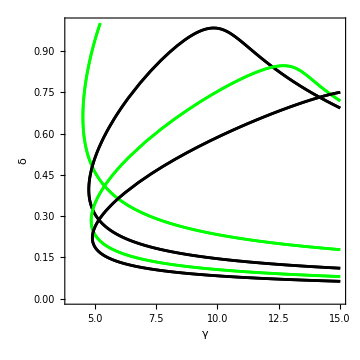

```mathematica
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]][[2]]]}],{critnum,Length[critchange]}];
]
bifcurveplot=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
bifcurveplot[[counter]]={};
For[outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
If[OddQ[lvalues[[counter]]],
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Green,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Black,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
];
AppendTo[bifcurveplot[[counter]],tempplot];
]
]
]
If[ValueQ[critpoints] && Length[critpoints]>0,
Row[(Show[#1,critpoints,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,critpoints,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
,
Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
```

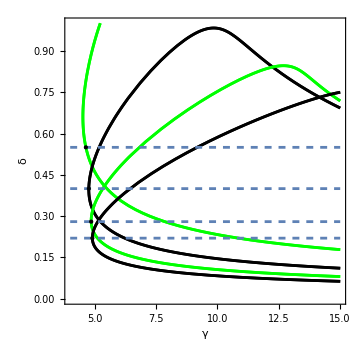

```mathematica
hl1=ParametricPlot[{t,0.55},{t,4,15},PlotStyle->Directive[Dashed]];
P1=Graphics[{PointSize[Large],Black,Point[{4.639433194901769,0.55}]}];
hl2=ParametricPlot[{t,0.4},{t,4,15},PlotStyle->Directive[Dashed]];
P2=Graphics[{PointSize[Large],Black,Point[{4.7580514243521215,0.4}]}];
hl3=ParametricPlot[{t,0.28},{t,4,15},PlotStyle->Directive[Dashed]];
P3=Graphics[{PointSize[Large],Black,Point[{4.855527499591434,0.28}]}];
hl4=ParametricPlot[{t,0.22},{t,4,15},PlotStyle->Directive[Dashed]];
P4=Graphics[{PointSize[Large],Black,Point[{4.902346005483433,0.22}]}];
(*hl5=ParametricPlot[{t,0.18},{t,4,15},PlotStyle->Directive[Dashed]];
P5=Graphics[{PointSize[Large],Black,Point[{4.928835063869236,0.18}]}];*)
Show[bifcurveplot,hl1,P1,hl2,P2,hl3,P3,hl4,P4,(*hl5,P5,*)PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
```

# Cross-order coefficient

```mathematica
counter=4;
auxsol={{par[[1]]->4.639433194901769,par[[2]]->0.55},
{par[[1]]->4.7580514243521215,par[[2]]->0.4},
{par[[1]]->4.855527499591434,par[[2]]->0.28},
{par[[1]]->4.902346005483433,par[[2]]->0.22}};
auxeq=eq/.auxsol[[counter]];
If[¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"],
Print["The cross-order coefficient will not be computed for l=" <> ToString[lvalues[[counter]]]];
,
simpleC11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
simpleC11=FormattingStrings[simpleC11];
factorC11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
factorC11=FormattingStrings[factorC11];
For[counterC11=1,counterC11<=2,counterC11++,
aux=ReadLine["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
aux2=ReadLine["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"];
If[counterC11==1,
crosspar=FormattingStrings[aux];
phieval=FormattingStringsCommaSplit[aux2];
,
termtodiff=FormattingStrings[aux];
psieval=FormattingStringsCommaSplit[aux2];
]
];
Close["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
Close["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"];
termtodiff=termtodiff/.eq;
termtodiff=D[termtodiff,crosspar];
For[varnum=0,varnum<=nvar-1,varnum++,
termtodiff=termtodiff/.Subscript[phiNF, varnum]->ToExpression[phieval[[varnum+1]],TeXForm];
termtodiff=termtodiff/.Subscript[psiNF, varnum]->ToExpression[psieval[[varnum+1]],TeXForm];
];
C11=simpleC11+factorC11*termtodiff/.fixedpar/.auxeq/.auxsol[[counter]];
]
```

```mathematica
C11
```

0.730658

```mathematica
C11
```

0.620246

```mathematica
C11
```

0.551339

```mathematica
C11
```

0.521154

# Getting points

```mathematica
parnum=2;
parval=0.4;
fixed={par[[parnum]]->parval};
actualt=Range[Length[zerodet]];
evaluations=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
actualt[[counter]]={};
evaluations[[counter]]={};
For [outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For [innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
tguess=Quiet@NSolve[par[[parnum]][time]-parval==0/.solutioncurves[[counter]][[outersolnum]][[innersolnum]],time];
For[solnum=1,solnum<=Length[tguess],solnum++,
If[Abs[par[[parnum]][time]-parval/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]]<tol,
AppendTo[actualt[[counter]],tguess];
AppendTo[evaluations[[counter]],Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]])},
Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),{varnum,2*nvar}]]]
]
]
]
]
]
```

# Amplitude equations

```mathematica
amplitudeequations=Range[Length[zerodet]];
C11=Range[Length[zerodet]];
For[counter=2,counter<=2(*Length[zerodet]*),counter++,
amplitudeequations[[counter]]=ConstantArray[0,2*lvalues[[counter]]+1];
For[mval=-lvalues[[counter]],mval<=lvalues[[counter]],mval++,
For[Subscript[q, 1]=-lvalues[[counter]],Subscript[q, 1]<=lvalues[[counter]],Subscript[q, 1]++,
For[Subscript[q, 2]=-lvalues[[counter]],Subscript[q, 2]<=lvalues[[counter]],Subscript[q, 2]++,
If[EvenQ[lvalues[[counter]]] && FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"],
C2=Import["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"];
C2expression=FormattingStrings[C2]/.fixedpar/.evaluations[[counter]][[1]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C2expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "}",TeXForm];
For[Subscript[q, 3]=-lvalues[[counter]],Subscript[q, 3]<=lvalues[[counter]],Subscript[q, 3]++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"],
C3=Import["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"];
C3expression=FormattingStrings[C3]/.fixedpar/.evaluations[[counter]][[1]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C3expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "} \\times A_{" <> ToString[Subscript[q, 3]] <> "}",TeXForm];
]
]
,
For[Subscript[q, 3]=-lvalues[[counter]],Subscript[q, 3]<=lvalues[[counter]],Subscript[q, 3]++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"],
C3=Import["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"];
C3expression=FormattingStrings[C3]/.fixedpar/.evaluations[[counter]][[1]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C3expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "} \\times A_{" <> ToString[Subscript[q, 3]] <> "}",TeXForm];
]
]
]
]
];
];
If[EvenQ[lvalues[[counter]]],
negativem=Table[Subscript[A, -m]->Subscript[B, m],{m,1,lvalues[[counter]]}];
positivem=Table[Subscript[A, m]->Subscript[A, -m],{m,1,lvalues[[counter]]}];
recover=Table[Subscript[B, m]->Subscript[A, m],{m,1,lvalues[[counter]]}];
For[eqnum=1,eqnum<=lvalues[[counter]],eqnum++,
amplitudeequations[[counter]][[eqnum]]=amplitudeequations[[counter]][[2*lvalues[[counter]]+1-(eqnum-1)]]/.negativem/.positivem/.recover;
]
];
If[¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"],
Print["The cross-order coefficient will not be computed for l=" <> ToString[lvalues[[counter]]]];
,
simpleC11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
simpleC11=FormattingStrings[simpleC11];
factorC11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
factorC11=FormattingStrings[factorC11];
For[counterC11=1,counterC11<=2,counterC11++,
aux=ReadLine["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
aux2=ReadLine["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"];
If[counterC11==1,
crosspar=FormattingStrings[aux];
phieval=FormattingStringsCommaSplit[aux2];
,
termtodiff=FormattingStrings[aux];
psieval=FormattingStringsCommaSplit[aux2];
]
];
Close["l=" <> ToString[lvalues[[counter]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
Close["l=" <> ToString[lvalues[[counter]]] <> "//Kernels.txt"];
termtodiff=termtodiff/.eq;
termtodiff=D[termtodiff,crosspar];
For[varnum=0,varnum<=nvar-1,varnum++,
termtodiff=termtodiff/.Subscript[phiNF, varnum]->ToExpression[phieval[[varnum+1]],TeXForm];
termtodiff=termtodiff/.Subscript[psiNF, varnum]->ToExpression[psieval[[varnum+1]],TeXForm];
];
C11[[counter]]=simpleC11+factorC11*termtodiff/.fixedpar/.evaluations[[counter]][[1]];
]
]
```

```mathematica
auxsol=NSolve[par[[2]][time]==0.55/.solutioncurves[[1]][[1]][[1]],time][[1]];
C31=Import["l=1//C3 q1=0, q2=0, q3=0, m=0.txt"];
C31=FormattingStrings[C31];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C31/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[1]][[1]][[1]]);
aval=toplot[time/.auxsol]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-0.380329

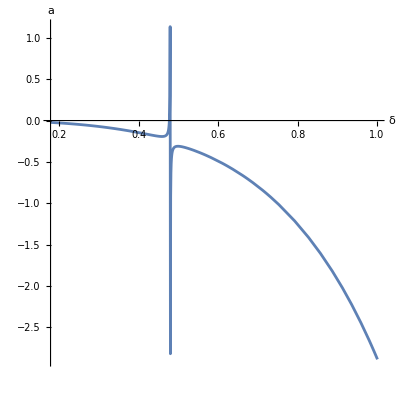

```mathematica
ParametricPlot[{par[[2]][time]/.solutioncurves[[1]][[1]][[1]],toplot[time]},{time,solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"δ","a"},BaseStyle->Directive[FontSize->15]]
```

```mathematica
auxsol=NSolve[par[[2]][time]==0.4/.solutioncurves[[2]][[1]][[1]],time][[1]];
C22=Import["l=2//C2 q1=0, q2=0, m=0.txt"];
C22=FormattingStrings[C22];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C22/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[2]][[1]][[1]]);
aval=-toplot[time/.auxsol]/2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-0.0132424

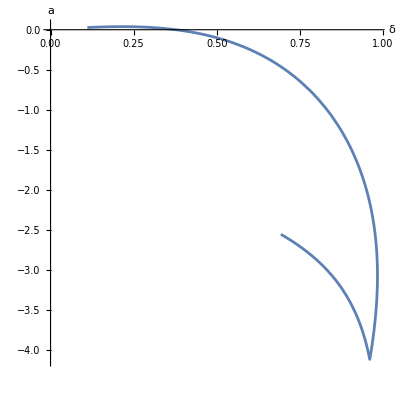

```mathematica
ParametricPlot[{par[[2]][time]/.solutioncurves[[2]][[1]][[1]],-toplot[time]/2},{time,solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"δ","a"},BaseStyle->Directive[FontSize->15]]
```

```mathematica
crit2=NSolve[toplot[time]==0,time][[1]];
{par[[1]][time],par[[2]][time]}/.solutioncurves[[2]][[1]][[1]]/.crit2
C32=Import["l=2//C3 q1=0, q2=0, q3=0, m=0.txt"];
C32=FormattingStrings[C32];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C32/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[2]][[1]][[1]]);
bval=-toplot[time/.crit2]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{4.76748,0.376823}

0.173063

```mathematica
auxsol=NSolve[par[[2]][time]==0.28/.solutioncurves[[3]][[1]][[1]],time][[1]];
C33=Import["l=3//C3 q1=1, q2=1, q3=1, m=3.txt"];
C33=FormattingStrings[C33];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C33/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[3]][[1]][[1]]);
aval=toplot[time/.auxsol]/(2*√15)
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.00128584

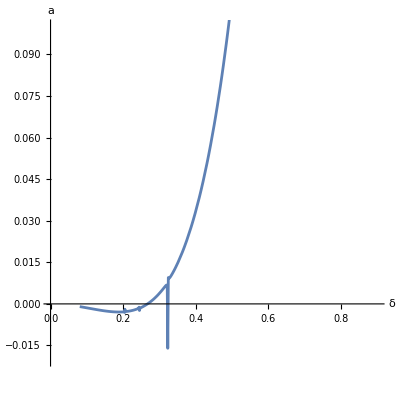

```mathematica
ParametricPlot[{par[[2]][time]/.solutioncurves[[3]][[1]][[1]],toplot[time]/(2*√15)},{time,solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"δ","a"},BaseStyle->Directive[FontSize->15],PlotRange->{{0,0.9},{-0.02,0.1}}]
```

```mathematica
C332=Import["l=3//C3 q1=0, q2=0, q3=3, m=3.txt"];
C332=FormattingStrings[C332];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C332/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[3]][[1]][[1]]);
bval=toplot[time/.auxsol]
```

-0.0785019

```mathematica
auxsol=NSolve[par[[2]][time]==0.22/.solutioncurves[[4]][[1]][[1]],time][[1]];
{par[[1]][time],par[[2]][time]}/.solutioncurves[[4]][[1]][[1]]/.auxsol;
C24=Import["l=4//C2 q1=0, q2=0, m=0.txt"];
C24=FormattingStrings[C24];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C24/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[4]][[1]][[1]]);
aval=toplot[time/.auxsol]/-18
crit2=NSolve[toplot[time]==0/.solutioncurves[[4]][[1]][[1]],time][[1]];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-0.000137086

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

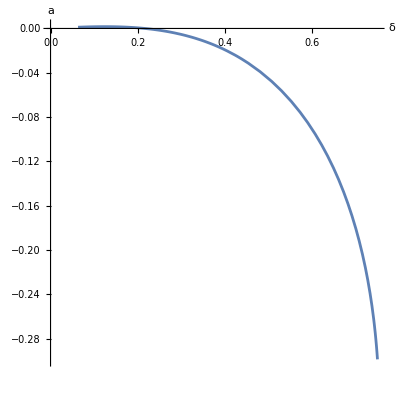

```mathematica
ParametricPlot[{par[[2]][time]/.solutioncurves[[4]][[1]][[1]],-toplot[time]/18},{time,solutioncurves[[4]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[4]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"δ","a"},BaseStyle->Directive[FontSize->15]]
```

```mathematica
C34=Import["l=4//C3 q1=-1, q2=2, q3=3, m=4.txt"];
C34=FormattingStrings[C34];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C34/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[4]][[1]][[1]]);
bval=toplot[time/.crit2]/210
```

0.0000758108

```mathematica
C342=Import["l=4//C3 q1=0, q2=0, q3=4, m=4.txt"];
C342=FormattingStrings[C342];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C342/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.solutioncurves[[4]][[1]][[1]]);
cval=toplot[time/.crit2]
```

-0.0480261

```mathematica
ϵval=0.01;
pareval={a->aval,b->bval,c->cval,ϵ->ϵval};
ss=Solve[ϵ==18*a*x+(160*b-c)*x^2,x]/.pareval//Expand
40*a*x-140*b*x^2/.ss/.pareval
60*a*x+90*b*x^2/.ss/.pareval
-10*a*x+160*b*x^2/.ss/.pareval
-18*a*x-320*b*x^2+2*c*x^2/.ss/.pareval
```

{{x→-0.387725},{x→0.428744}}

{0.000530533,-0.00430199}

{0.0042148,-0.00227228}

{0.00129195,0.00281745}

{-0.0190433,-0.0210579}

```mathematica
ss=Solve[ϵ==28*√14*a*x+(2240*b-24*c)*x^2,x]/.pareval//Expand
20*(√14*a*x-224*b*x^2)/.ss/.pareval
80*(√14*a*x-14*b*x^2)/.ss/.pareval
-4*(7*√14*a*x+1120*b*x^2-12*c*x^2)/.ss/.pareval
```

{{x→-0.0816976},{x→0.0925579}}

{-0.00142878,-0.00385913}

{0.00278569,-0.00452546}

{-0.0188267,-0.0213293}